## Useful functions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
Integrate[ x^2  (√((4 a^(3/2))/(√π)) Exp[-a x^2])^2,{x,0,Infinity}]
```

ConditionalExpression[1/(2 √2), Re[a]>0]

define a trail wave function with a set of {c_i,γ_i,δ_i}  with  ϕ(ρ_1,ρ_2)=(∑^N)_(i=1)c_i·e_^(-γ_i ρ_1^2-δ_i ρ_2^2)  and the  grid on which we evaluate this function

General::munfl: Exp[-19916.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4618.74] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-961.242] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-44577.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12491.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2817.94] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

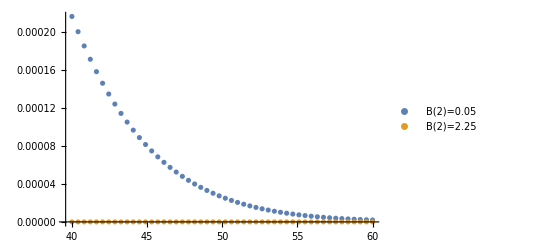

```mathematica
JacobiTrailWavefunctionParaU=
{{0.0509426,12.447514}, {0.0881925,2.886715} ,{0.130987,0.600776}, {0.205234,0.128325}, {0.388348,0.019765}, {0.577739,0.002348}};
JacobiTrailWavefunctionParaN=
{{0.0778620,27.860634},{0.160733,7.807216},{0.241234,1.761213},{0.304102,0.413738},{0.312105,0.112206},{0.222308,0.036085},{0.715921,0.012072}};
Rmax=3;
grdPoints=50;
r1r2Range=Subdivide[40,60,grdPoints-1];
JacobiTrailWavefunctionU=Total[#[[1]] √((4 #[[2]]^1.5)/(√π)) Exp[-#[[2]] r1^2]&/@JacobiTrailWavefunctionParaU];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,r1r2Range}];
JacobiTrailWavefunctionN=Total[#[[1]] √((4 #[[2]]^1.5)/(√π)) Exp[-#[[2]] r1^2]&/@JacobiTrailWavefunctionParaN];
JacobiTrailWavefunctionDataN=Table[JacobiTrailWavefunctionN/.{r1->R1},{R1,r1r2Range}];

ListPlot[{Transpose[{r1r2Range,JacobiTrailWavefunctionDataU}],Transpose[{r1r2Range,JacobiTrailWavefunctionDataN}]},PlotRange->Full,PlotLegends->{"B(2)=0.05","B(2)=2.25"}]
```

define the fit function  Φ(ρ_1,ρ_2)=(∑^nk)_(i=1)aLn_i·e_^(-bLn_i(ρ_1^2/4+ρ_2^2/3))

```mathematica
nk=5;
amin=-10;amax=10^3;
bmin=0;bmax=20000;
modelCluster={Sum[aLn@i Exp[-bLn@i (1./4. rrel1^2+1./3. rrel2^2)],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[JacobiTrailWavefunctionDataF,modelCluster,Flatten[Table[{{aLn@i,RandomReal[{-1.5,2.5}]},{bLn@i,RandomReal[{0.0001,5.25}]}},{i,nk}],1],{rrel1,rrel2}(*,Weights->((#+1)^1&/@data[[All,1]])*)]
```

FittedModel[3.72398 ⅇ^(-22.8815 (0.25 «1»+«1»))-«19» ⅇ^(«1»)+«1»-«1»+7.09132 ⅇ^(-«18» «1»)]

```mathematica
nlresi=nlmLABC["FitResiduals"];
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
basispara
ClusterWavefunctionData=Table[Normal[nlmLABC]/.{rrel1->R1,rrel2->R2},{R1,r1r2Range},{R2,r1r2Range}];
ListPlot3D[{ClusterWavefunctionData,JacobiTrailWavefunctionData},PlotStyle->{{Purple,Opacity[1.2]},{Green,Opacity[1.5]}},PlotLegends->{"Φ","ϕ"},PlotRange->Full,Mesh->None]
```

{{-9.98045,3.82972},{7.13245,5.86861},{3.72398,22.8815},{7.09132,2.93708},{-2.66002,7.36771}}

-Graphics3D-